#### Problem 3.

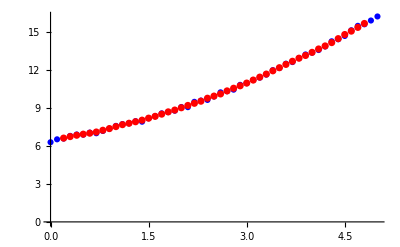
-Graphics-Position vs. Timetime, t (s)Position, x (m)

```mathematica
t={0.0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.0,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.0,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.0};
x ={6.29,6.52,6.58,6.79,6.9,6.89,7.05,7.00,7.18,7.36,7.58,7.72,7.78,7.95,7.91,8.18,8.34,8.57,8.67,8.78,9.07,9.06,9.48,9.58,9.63,9.9,10.23,10.32,10.44,10.82,10.95,11.2,11.39,11.63,11.98,12.15,12.49,12.62,12.93,13.22,13.36,13.57,13.85,14.26,14.42,14.68,15.13,15.48,15.6,15.9,16.22};
data=Transpose[{t,x}];
smoothedData = MovingAverage[data,5];
Dataplot=ListPlot[data,PlotStyle->Blue];
Labeled[Show[Dataplot, ListPlot[smoothedData,PlotStyle->Red ]],{"Position vs. Time","time, t (s)","Position, x (m)"},{Top,Bottom,Left},RotateLabel->True]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.917347 | 0.164819 | 5.56579 | 1.21457×10^-6
V | 0.421224 | 0.0573826 | 7.34064 | 2.49296×10^-9

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.822218 | 0.0515139 | 15.9611 | 1.11294×10^-19
V | 0.456535 | 0.0182854 | 24.9672 | 3.20886×10^-27

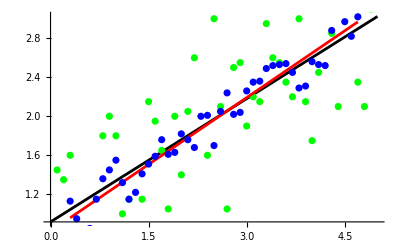
-Graphics-Velocity vs. Timetime, t (s)velocity, v (m/s)

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.822218 | 0.0515139 | 15.9611 | 1.11294×10^-19
V | 0.456535 | 0.0182854 | 24.9672 | 3.20886×10^-27

-Graphics-Velocity vs. Timetime, t (s)velocity, v (m/s)

```mathematica
v=Table[(x[[i+2]]-x[[i]])/(2dt),{i,1,Length[x]-2}]; 
dt=0.1;
t2=Table[t[[i]],{i,2,Length[x]-1}]; 
vdata=Thread[{t2,v}];
vfit=LinearModelFit[vdata,V,V];
vfitsmooth=LinearModelFit[vdatasmooth,V,V];
vfit["ParameterTable"]
vfitplot=Plot[vfit[X],{X,Min[t],Max[t]},PlotStyle->Black];
vplot=ListPlot[vdata,PlotStyle->Green];

xsmooth = MovingAverage[x,5];
tsmooth = MovingAverage[t,5];
vsmooth = Table[(xsmooth[[i+2]]-xsmooth[[i]])/(2dt),{i,1,Length[xsmooth]-2}]; 
tsmooth = Table[tsmooth[[i]],{i,2,Length[xsmooth]-1}]; 
vdatasmooth=Thread[{tsmooth,vsmooth}];
vfitsmooth=LinearModelFit[vdatasmooth,V,V];
vfitsmooth["ParameterTable"]
vfitplotsmooth=Plot[vfitsmooth[X],{X,Min[tsmooth],Max[tsmooth]},PlotStyle->Red];
vplotsmooth=ListPlot[vdatasmooth,PlotStyle->Blue];

Labeled[Show[vfitplot,vplot, vfitplotsmooth,vplotsmooth ],{"Velocity vs. Time","time, t (s)","velocity, v (m/s)"},{Top,Bottom,Left},RotateLabel->True]

vds=MovingAverage[v,5]; 
tds=MovingAverage[t2,5]; 
dt=0.1;
vdatads=Thread[{tds,vds}];
vfitds=LinearModelFit[vdatads,V,V];
vfitds["ParameterTable"]
vfitplotds=Plot[vfitds[X],{X,Min[tds],Max[tds]},PlotStyle->Red];
Labeled[vplotds=ListPlot[vdatads,PlotStyle->Blue],{"Velocity vs. Time","time, t (s)","velocity, v (m/s)"},{Top,Bottom,Left},RotateLabel->True];
Labeled[Show[vfitplot,vplot, vfitplotds,vplotds],{"Velocity vs. Time","time, t (s)","velocity, v (m/s)"},{Top,Bottom,Left},RotateLabel->True]
```

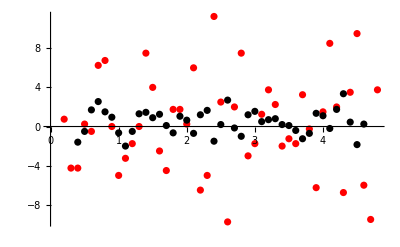
-Graphics-Acceleration vs. Timetime, t (s)Acceleration, a (m/s^2)

Mean Accelaration: 0.255319 | STD: 4.91545 | Smoothed Mean Accelaration: 0.437209 | Smoothed STD: 1.23168

```mathematica
a=Table[(v[[i+2]]-v[[i]])/(2dt),{i,1,Length[v]-2}]; 
t3=Table[t2[[i]],{i,2,Length[v]-1}]; 
adata=Thread[{t3,a}];
aplot=ListPlot[adata,PlotStyle->Red];

as=Table[(vsmooth[[i+2]]-vsmooth[[i]])/(2dt),{i,1,Length[vsmooth]-2}]; 
ts=Table[tsmooth[[i]],{i,2,Length[vsmooth]-1}]; 
adatas=Thread[{ts,as}];
Labeled[Show[aplot,aplots=ListPlot[adatas,PlotStyle->Black]],{"Acceleration vs. Time","time, t (s)","Acceleration, a (m/s^2)"},{Top,Bottom,Left},RotateLabel->True]
Print[ " Mean Accelaration: ",Mean[a],
 " | STD: ",StandardDeviation[a] ,
" | Smoothed Mean Accelaration: ",Mean[as],
 " | Smoothed STD: ", StandardDeviation[as]]
```

| Estimate | Standard Error | t-Statistic | P-Value
a0 | 6.41418 | 0.0302922 | 211.743 | 5.74196×10^-73
a1 | 0.855848 | 0.0280186 | 30.5457 | 4.15741×10^-33
a2 | 0.444292 | 0.0108384 | 40.9923 | 5.14572×10^-39

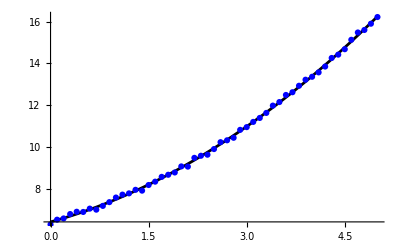

```mathematica
xfit=NonlinearModelFit[data,a0+a1 X+1/2 a2 X^2,{a0,a1,a2},X];
xfit["ParameterTable"]
xfitplot=Plot[xfit[X],{X,Min[t],Max[t]},PlotStyle->Black];
Show[xfitplot,Dataplot]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.917347 | 0.164819 | 5.56579 | 1.21457×10^-6
V | 0.421224 | 0.0573826 | 7.34064 | 2.49296×10^-9

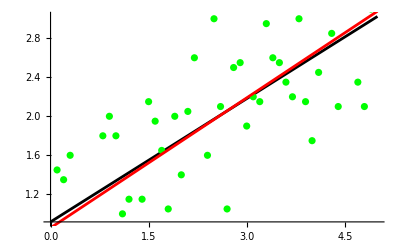

```mathematica
vfit=LinearModelFit[vdata,V,V];
vfit["ParameterTable"]
vfitplot=Plot[vfit[X],{X,Min[t],Max[t]},PlotStyle->Black];
dvplot=Plot[(D[xfit[X],X]/.X->T),{T,Min[t],Max[t]},PlotStyle->Red];
Show[vfitplot,vplot, dvplot]
```

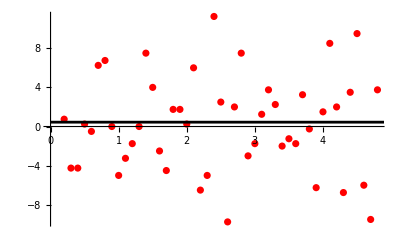

```mathematica
daplot=Plot[D[xfit[X],{X,2}]/.X->T,{T,Min[t],Max[t]},PlotStyle->Black];
Show[aplot, daplot]
```

#### Problem 4.

Spring Constant k = 0.364286 N/cm

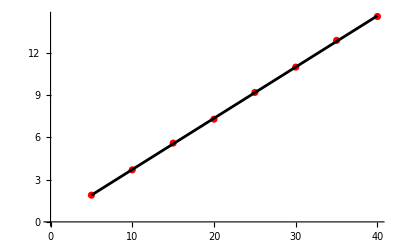

```mathematica
x={5.0,10.0,15.0,20.0,25.0,30.0,35.0,40.0};
F={1.9,3.7,5.6,7.3,9.2,11.0,12.9,14.6};
data = Thread[{x,F}];
lmf=LinearModelFit[data, X, X];
k=lmf["BestFitParameters"][[2]];
Print["Spring Constant k = ",k," N/cm"];
dataplot = ListPlot[data, PlotStyle->Red];
fitplot = Plot[lmf[X],{X, Min[x],Max[x]}, PlotStyle->Black];
Show[dataplot, fitplot]
```

```mathematica
rectangles=Table[x[[i]] (F[[i+1]]-F[[i]]),{i,1,Length[F]-1}];  (* Create a rectangular approximation to the integral*)
intrect=Total[rectangles]
```

253.

```mathematica
trapezoids=Table[(x[[i]]+x[[i+1]])/2(F[[i+1]]-F[[i]]),{i,1,Length[F]-1}];  (* Create a trapezoidal approximation to the integral*)
inttrap=Total[trapezoids]
```

284.75

```mathematica
F=1/2 k*(Max[x])^2
```

291.429

```mathematica
int=Integrate[lmf[X],{X, Min[x],Max[x]}]
```

289.625

```mathematica
(* Comparing to results from the known function *)
```

```mathematica
Print[Column[{"Percent Difference:",Row[{"Rectangular Integration: ",Abs[intrect-F]/F*100,"%"}],Row[{"Trapezoidal Integration: ",Abs[inttrap-F]/F*100,"%"}],
Row[{"Linear Model Fit: ",Abs[int-F]/F*100,"%"}]},Spacings->1]]
```

Percent Difference:
Rectangular Integration: 13.1863%
Trapezoidal Integration: 2.29167%
Linear Model Fit: 0.618873%